The car is behind door 1. All other cases are symmetric and have the same probabilities.

```mathematica
firstChoice[]:=RandomInteger[{1,3}];
montyChoice[yourFirst_]:=
If[yourFirst===1,
RandomInteger[{2,3}],
(* else *) 5-yourFirst];
secondChoice[yourFirst_,montyChoice_,switchQ_]:=
If[switchQ,
Switch[yourFirst,
1,5-montyChoice,
2,1,
3,1],
yourFirst];
```

```mathematica
round[switchQ_]:=
With[{f=firstChoice[]},
With[{m=montyChoice[f]},
secondChoice[f,m,switchQ]]];
```

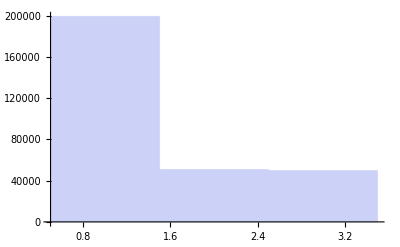

```mathematica
Histogram[Table[round[True],{300000}],{0.5,3.5,1}]
```

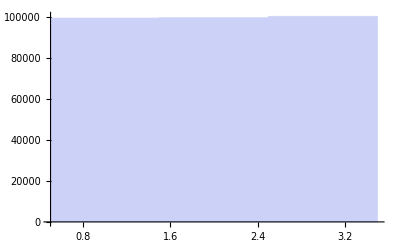

```mathematica
Histogram[Table[round[False],{300000}],{0.5,3.5,1}]
```